```mathematica
outputdir="/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode/";
```

{{:0,:1,:2},{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

{{3.,0,0},{2.9,0,0},{2.8,0,0},{2.7,0,0},{2.6,0,0},{2.5,0,0},{2.4,0,0},{2.3,0,0},{2.2,0,0},{2.1,0,0},{2.,0,0},{1.9,0,0},{1.8,0,0},{1.7,0,0},{1.6,0,0},{1.5,0,0},{1.4,0,0},{1.3,0,0},{1.2,0,0},{1.1,0,0},{1.,0,0}}

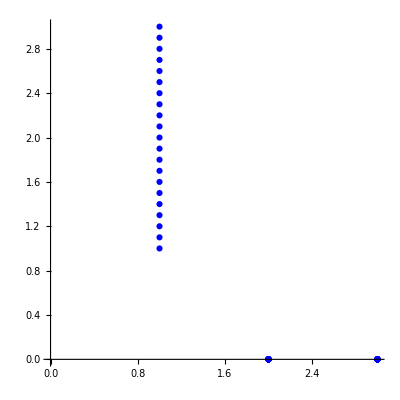

21

```mathematica
tabve=Import["/Users/michelecastellana/Documents/finite_elements/generate_mesh/1d/line/solution/vertices.csv"]
tabve=Table[tabve[[i]],{i,2,Length[tabve]}]
ListPlot[tabve,PlotStyle->Blue,AspectRatio->1]
Length[tabve]
```

```mathematica
(*write ψ from ODE to csv file*)
```

```mathematica
tabψ=Table[{ψ[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabψ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.5,3.,0,0},{2.24206,2.9,0,0},{1.85482,2.8,0,0},{1.35589,2.7,0,0},{0.786918,2.6,0,0},{0.210025,2.5,0,0},{-0.313873,2.4,0,0},{-0.746826,2.3,0,0},{-1.0778,2.2,0,0},{-1.31308,2.1,0,0},{-1.46552,2.,0,0},{-1.54831,1.9,0,0},{-1.57258,1.8,0,0},{-1.54713,1.7,0,0},{-1.4789,1.6,0,0},{-1.37381,1.5,0,0},{-1.23742,1.4,0,0},{-1.07543,1.3,0,0},{-0.894055,1.2,0,0},{-0.699942,1.1,0,0},{-0.5,1.,0,0}}

```mathematica
Export[outputdir<>"psi.csv",tabψ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode/psi.csv

```mathematica
(*write μ from ODE to csv file*)
```

```mathematica
tabμ=Table[{H[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabμ,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{-0.344183,3.,0,0},{-0.60208,2.9,0,0},{-0.860635,2.8,0,0},{-1.08072,2.7,0,0},{-1.20504,2.6,0,0},{-1.19744,2.5,0,0},{-1.07389,2.4,0,0},{-0.885515,2.3,0,0},{-0.680083,2.2,0,0},{-0.48404,2.1,0,0},{-0.305747,2.,0,0},{-0.144062,1.9,0,0},{0.0054917,1.8,0,0},{0.147552,1.7,0,0},{0.285524,1.6,0,0},{0.421031,1.5,0,0},{0.553791,1.4,0,0},{0.681794,1.3,0,0},{0.801771,1.2,0,0},{0.909937,1.1,0,0},{1.00287,1.,0,0}}

```mathematica
Export[outputdir<>"mu.csv",tabμ]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode/mu.csv

```mathematica
(*write X from ODE to csv file*)
```

```mathematica
tabX=Table[Flatten[{{X1[x],X2[x],0}/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]}],{i,1,Length[tabve]}];
PrependTo[tabX,{"f:0","f:1","f:2",":0",":1",":2"}]
```

```mathematica
Export[outputdir<>"X.csv",tabX]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode/X.csv

```mathematica
(*write ν from ODE to csv file*)
```

```mathematica
tabν=Table[{ν[x]/.s/.{x->tabve[[i,1]]},tabve[[i,1]],tabve[[i,2]],tabve[[i,3]]},{i,1,Length[tabve]}];
PrependTo[tabν,{"f",":0",":1",":2"}]
```

{{f,:0,:1,:2},{2.77948,3.,0,0},{2.6905,2.9,0,0},{2.60153,2.8,0,0},{2.51256,2.7,0,0},{2.42358,2.6,0,0},{2.33461,2.5,0,0},{2.24563,2.4,0,0},{2.15666,2.3,0,0},{2.06769,2.2,0,0},{1.97871,2.1,0,0},{1.88974,2.,0,0},{1.80076,1.9,0,0},{1.71179,1.8,0,0},{1.62282,1.7,0,0},{1.53384,1.6,0,0},{1.44487,1.5,0,0},{1.3559,1.4,0,0},{1.26692,1.3,0,0},{1.17795,1.2,0,0},{1.08897,1.1,0,0},{1.,1.,0,0}}

```mathematica
Export[outputdir<>"nu.csv",tabν]
```

/Users/michelecastellana/Documents/finite_elements/steady_state/no_flow/lagrangian_approach/one_dimension/solution_ode/nu.csv